0.000058745 √t

330.865+192.135 ⅇ^(-0.014649 tt)

t_c

330.865+192.135 ⅇ^(-0.014649 t_c)

{(1.549×10^6 (192.135-192.135 ⅇ^(-0.014649 τ)))/τ,(286.441 (192.135-192.135 ⅇ^(-0.014649 t_c)))/t_c^2,0.,64500. (-333+T_surf),(2.13533×10^6 (0.000059+0.00119063 t_c) (-293+T_surf))/t_c,(0.0272414 (-7370050801+T_surf^4))/t_c}

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

(1. | (5407.75 (192.135-192.135 2.71828^(-0.014649 τ)) t_c^2)/((192.135-192.135 2.71828^(-0.014649 t_c)) τ) | ComplexInfinity | (24.0155 (192.135-192.135 2.71828^(-0.014649 τ)))/(τ (-333.+T_surf)) | (0.725416 (192.135-192.135 2.71828^(-0.014649 τ)) t_c)/(τ (0.000059+0.00119063 t_c) (-293.+T_surf)) | (5.68619×10^7 (192.135-192.135 2.71828^(-0.014649 τ)) t_c)/(τ (-7.37005×10^9+T_surf^4))
(0.00018492 (192.135-192.135 2.71828^(-0.014649 t_c)) τ)/((192.135-192.135 2.71828^(-0.014649 τ)) t_c^2) | 1. | ComplexInfinity | (0.00444094 (192.135-192.135 2.71828^(-0.014649 t_c)))/(t_c^2 (-333.+T_surf)) | (0.000134144 (192.135-192.135 2.71828^(-0.014649 t_c)))/((0.000059+0.00119063 t_c) t_c (-293.+T_surf)) | (10514.9 (192.135-192.135 2.71828^(-0.014649 t_c)))/(t_c (-7.37005×10^9+T_surf^4))
0. | 0. | Indeterminate | 0. | 0. | 0.
(0.0416398 τ (-333.+T_surf))/(192.135-192.135 2.71828^(-0.014649 τ)) | (225.178 t_c^2 (-333.+T_surf))/(192.135-192.135 2.71828^(-0.014649 t_c)) | ComplexInfinity | 1. | (0.0302062 t_c (-333.+T_surf))/((0.000059+0.00119063 t_c) (-293.+T_surf)) | (2.36772×10^6 t_c (-333.+T_surf))/(-7.37005×10^9+T_surf^4)
(1.37852 τ (0.000059+0.00119063 t_c) (-293.+T_surf))/((192.135-192.135 2.71828^(-0.014649 τ)) t_c) | (7454.69 (0.000059+0.00119063 t_c) t_c (-293.+T_surf))/(192.135-192.135 2.71828^(-0.014649 t_c)) | ComplexInfinity | (33.1058 (0.000059+0.00119063 t_c) (-293.+T_surf))/(t_c (-333.+T_surf)) | 1. | (7.83853×10^7 (0.000059+0.00119063 t_c) (-293.+T_surf))/(-7.37005×10^9+T_surf^4)
(1.75865×10^-8 τ (-7.37005×10^9+T_surf^4))/((192.135-192.135 2.71828^(-0.014649 τ)) t_c) | (0.0000951032 t_c (-7.37005×10^9+T_surf^4))/(192.135-192.135 2.71828^(-0.014649 t_c)) | ComplexInfinity | (4.22348×10^-7 (-7.37005×10^9+T_surf^4))/(t_c (-333.+T_surf)) | (1.27575×10^-8 (-7.37005×10^9+T_surf^4))/((0.000059+0.00119063 t_c) (-293.+T_surf)) | 1.)

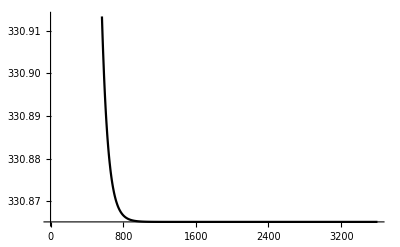

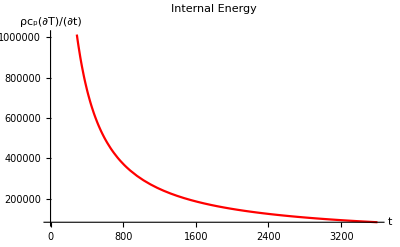

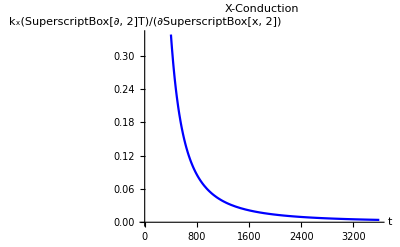

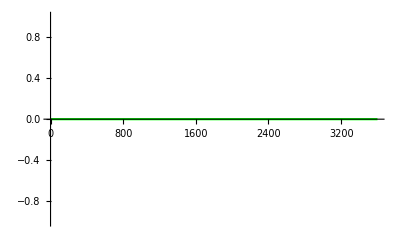

-Graphics-

-Graphics-

-Graphics-

```mathematica
rhocp=1.549*(10^6);
T1=493;
T2=276;
delT=T1-T2;
u=0.0635;
xx=u*Subscript[t, c];
k=1.3;
dnozzle=0.00762;
height=2*10^-3;
w=14.75*10^-3;
Vv=height*xx*w;
hh=4;
Aa=xx*w+2*w*height+2*xx*height;
epsilon=0.9;
sigma=5.67*(10^(-8));
Subscript[T, extruder]=250+273;
Subscript[T, bed]=60+273;
Subscript[T, ∞]=20+273;
kx=1.155;
ky=0.488;
kz=0.258;

kabs=(kx+ky+kz)/3;
alll=kabs/rhocp;
el=(w+height)/2;
ratio1=(el^2)/(alll*ttt);
ratio2=(1/u)*Sqrt[alll/t];
ratio3=(alll*Sqrt[alll*t])/(u*el^2)
Ti=Subscript[T, extruder];
Tamb=Subscript[T, ∞];
Tavg=(Ti+Tamb)/2;
Tb=Subscript[T, bed];

a1=Ti-(hh*height*Tamb+kabs*Tb+4*height*epsilon*sigma*Tavg^3*Tamb)/(hh*height+kabs+4*height*epsilon*sigma*Tavg^3);
b1=-(hh*w*w*height+kabs*w*w+4*w*w*height*epsilon*sigma*Tavg^3)/(rhocp*w^3*height);
c1=(hh*height*Tamb+kabs*Tb+4*height*epsilon*sigma*Tavg^3*Tamb)/(hh*height+kabs+4*height*epsilon*sigma*Tavg^3);
temprad[tt_]=a1*Exp[tt*b1]+c1
 Subscript[t, c]
temprad[Subscript[t, c]]
ΔT=Ti-temprad[τ];


termVec={(rhocp*ΔT)/(τ),(kx*(Subscript[T, extruder]-temprad[Subscript[t, c]]))/(xx^2),(ky*0)/(w^2),(kz*(Subscript[T, surf]-Subscript[T, bed]))/(height^2),(hh*Aa*(Subscript[T, surf]-Subscript[T, ∞]))/(Vv),(epsilon*sigma*(Subscript[T, surf]^4-Subscript[T, ∞]^4))/(Vv)}

compare={};
compareRow={};
For[i=1,i≤Length[termVec],i++,
For[j=1,j≤Length[termVec],j++,
AppendTo[compareRow,termVec[[i]]/termVec[[j]]];
];
AppendTo[compare,compareRow];
compareRow={};
]
compare//N//MatrixForm
Plot[temprad[Subscript[t, c]],{Subscript[t, c],0,3600},PlotStyle->Black]
Plot[termVec[[1]],{τ,0,3600},PlotStyle->Red,AxesLabel->{t,"ρc_p(∂T)/(∂t)"},PlotLabel->"Internal Energy"]
Plot[termVec[[2]],{Subscript[t, c],0,3600},PlotStyle->Blue,AxesLabel->{t,"k_x(SuperscriptBox[∂, 2]T)/(∂SuperscriptBox[x, 2])"},PlotLabel->"X-Conduction"]
Plot[termVec[[3]],{τ,0,3600},PlotStyle->Green]
Plot[termVec[[4]],{τ,0,3600},PlotStyle->Orange]
Plot[termVec[[5]],{τ,0,360},PlotStyle->Purple]
Plot[termVec[[6]],{τ,0,3600},PlotStyle-> Black]
```

```mathematica
{(1.549*^6 (192.13486254975157-192.13486254975157 ⅇ^(-0.01464899673091544 τ)))/τ,(286.4405728811458 (192.13486254975157-192.13486254975157 ⅇ^(-0.01464899673091544 Subscript[t, c])))/Subscript[t, c]^2,0.,64500. (-333+Subscript[T, surf]),(2.135326304550914*^6 (0.000059000000000000004+0.001190625 Subscript[t, c]) (-293+Subscript[T, surf]))/Subscript[t, c],(0.027241425330308287 (-7370050801+Subscript[T, surf]^4))/Subscript[t, c]}
```